```mathematica
Enter the Mathematica  package.
```

```mathematica
<<D:\\Economics\Courses\MGSC533\2017\Math\Spurious\Spurious.m
```

```mathematica
The function SpuriousEst returns two sequences 
generated by the equation 
p_{t+1} = p_t + c (pStar - p_t) + e_t .
```

```mathematica
If we call the elements of the first 
sequence p1_t and the second sequence p2_t 
then the function also returns pairs of observations 
(p1_t, p2_t) for t = 0, 1, 2, 3,..., n.
```

```mathematica
After the pairs of observations it returns the 
estimation from the regression of p2_t on p1_t.
```

```mathematica
(* Inputs for SpuriousEst are c, p0, pStar, n, const.   *)
(* The length of the random walk is 'n'.  If const = 1  *)
(* then there is a constant in the regression.          *)
```

```mathematica
output = SpuriousEst[0.0,0,0,100, 1];
```

```mathematica
(* The main output of SpuriousEst is the table with     *)
(* regression coefficients and p-values.                *)
```

```mathematica
output[[4]]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -10.5019 | 0.524839 | -20.0097 | 2.19274×10^-36
x | -0.12225 | 0.0541545 | -2.25742 | 0.0262011

```mathematica
The pairs (p1_t, p2_t) can be graphed with p1 on the 
horizontal axis and p2 on the vertical axis.
```

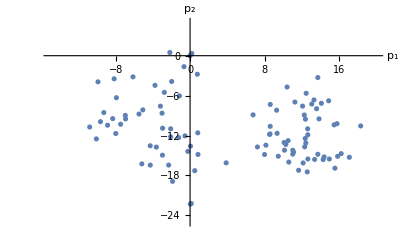

```mathematica
ListPlot[output[[3]], PlotRange -> {output[[7]], output[[6]]}, AxesLabel -> {Subscript["p", 1], Subscript["p", 2]}]
```

```mathematica
The estimated relationship between these variables 
is shown as a line.  The p-value for the significance of 
the relationship between the two variables  is the number 
in the lower right hand side of the table shown in the 
output from SpuriousEst.
```

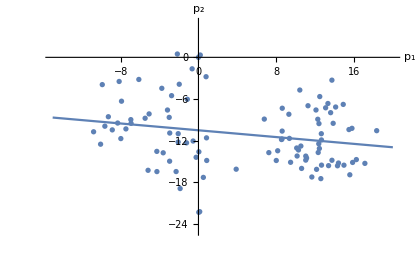

```mathematica
Show[ListPlot[output[[3]], PlotRange -> {output[[7]], output[[6]]}, AxesLabel -> {Subscript["p", 1], Subscript["p", 2]}],Plot[output[[5,1]] + output[[5, 2]] * x, {x, output[[7, 1]], output[[7, 2]]}]]
```

```mathematica
(*  This is the graph of the sequence of 'y' observations.   *)
```

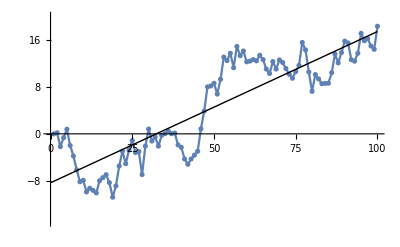

```mathematica
Show[ListPlot[output[[2]], PlotRange -> output[[7]]], ListPlot[output[[2]], Joined -> True], Graphics[Line[f[output[[2]]]]]]
```

```mathematica
(*  This is the graph of the sequence of 'x' observations.   *)
```

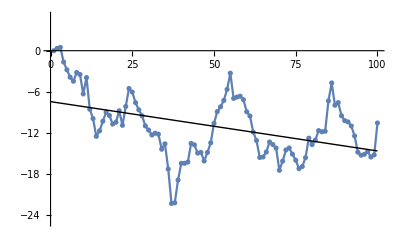

```mathematica
Show[ListPlot[output[[1]], PlotRange -> output[[6]]], ListPlot[output[[1]], Joined -> True], Graphics[Line[f[output[[1]]]]]]
```

```mathematica
The Durbin-Watson statistic is a diagnostic to 
determine  whether data are serially correlated.
```

```mathematica
Critical values  for the statistic can be found in the 
handout that I gave to you on the first day of class.
```

```mathematica
Durbin[output[[2]]]
```

0.225623

```mathematica
Durbin[output[[1]]]
```

0.183815

```mathematica
The function SpuriousSignificance takes inputs 
(c, p0, pStar, n, const, N) and determines how 
many of the N simulations with sequences of length 
n and with adjustment rate c appear to be related.
```

```mathematica
SpuriousSignificance[0.0,0,0,25,1,1000]
```

0.528

```mathematica
Even with very short sequences (n = 25) the 
number is close to 50%.
```

```mathematica
SpuriousSignificance[0.0,0,0,100,1,1000]
```

0.765

```mathematica
With longer sequences the fraction of the pairs 
of sequences that appear to be related increases.
```

```mathematica
SpuriousSignificance[0.0,0,0,200,1,1000]
```

0.834

```mathematica
SpuriousSignificance[0.0,0,0,400,1,1000]
```

0.867